# 28: Basic QR Algorithm on our way to Francis Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

```mathematica
SetOptions[MatrixPlot,ColorRules->{0->Green}];
```

## Motivational Demo

The book says “Compute the QR decomposition, flip the order of the factors and repeat!”. Here is an example for a tridiagonal symmetric matrix T.

```mathematica
m=7; MaxIter=17;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
TabView[
Table[
{Q,R}=QRDecomposition[T];Q=Qᵀ;
T=Chop[R.Q];
MatrixPlot[T],
{MaxIter}]
]
```

1234567891011121314151617

Lets look at the first and last “T” matrices

```mathematica
TabView[{
"T_0"->MatrixForm[T0],
"T_last"->MatrixForm[T]}]
Eigenvalues[A]
```

12

{-4.78894,3.76158,-2.09626,-1.41222,1.27879,-0.6206,0.532435}

It is pretty clear that something is driving the off-diagonals to zero: this means the diagonals are heading to the eigenvalues!  We want to understand what is doing this. Once we understand that we might be able to make it go faster! In a fit of bravado, we are going to guess at something that makes it go faster

### Shifts

After a few steps we should have a vague idea of some of the eigenvalues! There should be a way of incorporating these estimates into the algorithm.

Obvious Fact #42:
If the eigenvalues of A are {λ_1,λ_2,…,λ_m} then the eigenvalues of A-μ I_m are simply {λ_1-μ,λ_2-μ,…,λ_m-μ}
This is called a shift.

Less Obvious Observation:
If μ is an eigenvalue then one QR step on “T-μ I_m" makes the problem gets smaller. 
This is called “Deflation”.

{3.65165,-3.33165,-2.77541,2.37784,-2.01723,1.40859,0.0632525}

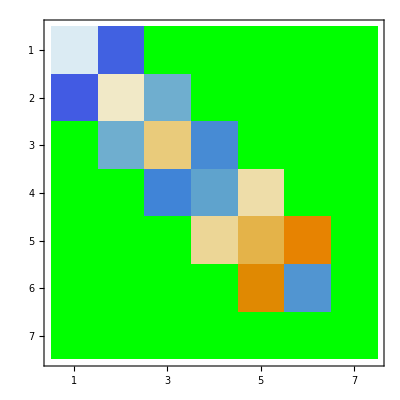

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
μ=RandomChoice[λs];
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
Eigenvalues[T]+μ
MatrixPlot[T]
```

It does not have to be exact to be useful! The cheesiest guess we have at an eigenvalue is the last diagonal entry! Even this simple “shift” strategy helps a lot.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
TabView[{
"T_0"->MatrixPlot[T0],
"T_1"->MatrixPlot[T]}]
TabView[{
"T_0"->MatrixForm[T0],
"T_1"->MatrixForm[T]}]
```

12

12

I guess we should throw this into our code and see if it is faster! The one missing ingredient is that we need to add the shift back in if we want to combine steps. Here is our new code!

```mathematica
m=7; MaxIter=4;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
Id=IdentityMatrix[m];
TabView[
Table[
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ Id];Q=Qᵀ;
T=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(-2.56435 | -0.84253 | 0 | 0 | 0 | 0 | 0
-0.84253 | 3.07919 | -1.3205 | 0 | 0 | 0 | 0
0 | -1.3205 | -0.569614 | -0.195987 | 0 | 0 | 0
0 | 0 | -0.195987 | -0.9851 | -0.452382 | 0 | 0
0 | 0 | 0 | -0.452382 | 1.51841 | -1.30079 | 0
0 | 0 | 0 | 0 | -1.30079 | 0.877019 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.940861)

It almost always immediately resolves an eigenvalue at the bottom corner!  Of course, the shift stops doing any good once that has happened! If we want to continue effectively we need to work out how to “deflate” the converged elements. In general, deflation involves slightly complicated bookkeeping. Our book wimps out on “deflation”. I am going to try to show what happens when the bottom deflates!

### Deflation

Lets decide that the bottom diagonal “eigenvalue” is resolved when the ratio of the off-diagonal element to the diagonal element is less than some tolerance.  Our bookkeeping consists of a single number “n” that is the number of eigenvalues still to be resolved. I am going to call this the active dimension.  Of course, n starts at m and the code decreases it as appropriate.

```mathematica
m=8; MaxIter=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
Eigenvalues[A]
```

123456789101112

(-3.96164 | -0.0233913 | 0 | 0 | 0 | 0 | 0 | 0
-0.0233913 | 3.18919 | -0.0565184 | 0 | 0 | 0 | 0 | 0
0 | -0.0565184 | -1.70791 | -0.00997936 | 0 | 0 | 0 | 0
0 | 0 | -0.00997936 | -1.17628 | -0.105952 | 0 | 0 | 0
0 | 0 | 0 | -0.105952 | 1.63564 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.256269 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.863812 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.438983)

{-3.96171,3.18992,-1.70875,1.63962,-1.18008,0.863812,0.438983,-0.256269}

### Better Shift

This simplest shift does not always work!  For instance, the tridiagonal matrix 
	T=(2 | 0 |  
0 | 0 | 1
  | 1 | 0)
is unchanged by an unshifted QR step!

```mathematica
T=({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}});
{Q,R}=QRDecomposition[T];Q=Qᵀ;
MatrixForm[R.Q]
```

(2 | 0 | 0
0 | 0 | 1
0 | 1 | 0)

Clearly adding a shift of μ=T_(3,3)=0 does not change the situation. The problem is that the bottom two eigenvalues are ±1 and our current algorithm can not resolve the symmetry.  The solution called a Wilkinson shift is to choose the eigenvalue of the bottom 2×2 matrix nearest the bottom entry.

Here is a demo of the “bad” matrix breaking the Rayleigh shift.

```mathematica
m=3; MaxIter=4;
T0=T=N[({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}})];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(2. | 0 | 0
0 | 0 | 1.
0 | 1. | 0)

Here is the Wilkinson shift code

```mathematica
m=3; MaxIter=3;
T0=T=N[({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}})];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Wilikinson Shift *)
If[n>1,
{μ1,μ2}=Eigenvalues[T⟦n-1;;n,n-1;;n⟧];
μ=Sort[ {μ1,μ2}, Abs[#1-T⟦n,n⟧]≤Abs[#2-T⟦n,n⟧]&]⟦1⟧,
μ=T⟦n,n⟧];
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

123

(2. | 0 | 0
0 | 1. | 0
0 | 0 | -1.)

### Racing Shifts

We have two different shifts: Wilkinson and Rayleigh.  The obvious question is which is faster.  easy enough to answer with our assorted code fragments.

```mathematica
m=23; MaxIter=18;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
T0=Chop[HessenbergDecomposition[A]⟦2⟧];
(* Initialize the Active Dimension *)
n=m; T=T0; Tol=10^-12;
Wilkinson =TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Wilikinson Shift *)
If[n>1,
{μ1,μ2}=Eigenvalues[T⟦n-1;;n,n-1;;n⟧];
μ=Sort[ {μ1,μ2}, Abs[#1-T⟦n,n⟧]≤Abs[#2-T⟦n,n⟧]&]⟦1⟧,
μ=T⟦n,n⟧];
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}],MaxIter];
n=m; T=T0;
Rayleigh =TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Rayleigh Shift *)
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}],MaxIter];
TabView[{
"Rayleigh"->Rayleigh,
"Wilkinson"->Wilkinson
}]
```

12

Wilkinson (almost) always wins.  Rayleigh can stall. Wilkinson is better.

## Convergence of QR

So why does this work?

### Block Power Method aka Simultaneous Iteration (SI)

We can compute the two “largest” eigenvectors by doing two vectors at the same time in the power method.  To keep the two vectors from collapsing to the “largest” of the two vectors orthogonalize with a QR at every step.

The same though process would work with a block of three or more vectors. In the animation below you can see the first column lock first (the largest eigenvector) followed by the second and third eigenvectors.

```mathematica
{m,b}={23,3};
A=Symmetrize[RandomReal[{-1,1},{m,m}]];
V0=QRDecomposition[RandomReal[{-1,1},{m,b}]]⟦1⟧ᵀ;
MaxIter=123;
BlockData=NestList[ QRDecomposition[A.#]⟦1⟧ᵀ&,V0,MaxIter];
ListAnimate[Map[MatrixPlot,BlockData],4]
```

You can write down a convergence result just like the power method using the gaps between the eigenvalues.

```mathematica
Eigenvectors[A,3]
BlockData⟦-1⟧
```

{{-0.0386903,-0.202862,0.256605,0.236061,0.0792537,0.0170251,-0.375739,-0.0952761,0.230926,-0.0527759,-0.212276,-0.167171,-0.107184,0.0441914,0.33555,-0.386543,0.370009,0.0391203,-0.182404,-0.258325,0.0808701,-0.146783,-0.0886283},{0.280275,0.0802501,0.388415,-0.00580126,-0.309864,0.254933,0.243646,-0.00537381,0.34036,0.0302225,-0.179014,-0.147314,-0.118568,0.0512175,-0.164797,-0.0396294,0.0783351,-0.324624,0.114136,0.241218,-0.30391,-0.191459,0.126661},{0.040431,-0.110203,-0.155765,-0.371703,0.206415,-0.0507931,0.179677,-0.265041,0.130379,-0.260793,0.0225553,-0.154481,-0.433341,0.299999,-0.211515,-0.247741,0.0280341,0.206428,-0.202759,0.0575129,-0.126881,0.272475,0.0680754}}

{{-0.0384537,0.139704,-0.246371},{-0.202714,-0.0733435,-0.11502},{0.257073,-0.00341624,-0.418088},{0.236303,-0.348726,-0.129729},{0.0788247,0.080372,0.364093},{0.0172985,0.0454396,-0.255925},{-0.375629,0.25592,-0.161986},{-0.0951056,-0.248438,-0.0913983},{0.231159,0.245196,-0.269384},{-0.0525743,-0.232036,-0.123133},{-0.212459,-0.0450446,0.174428},{-0.167207,-0.197933,0.0806912},{-0.107008,-0.446713,-0.0473191},{0.0440404,0.298162,0.061524},{0.335535,-0.257005,0.0768759},{-0.386416,-0.244681,-0.0534593},{0.370064,0.0548073,-0.0623222},{0.0386779,0.0744215,0.377608},{-0.182163,-0.14707,-0.180186},{-0.258136,0.140952,-0.204151},{0.0806687,-0.229029,0.236907},{-0.147144,0.183863,0.277235},{-0.088554,0.109081,-0.0934382}}

### Connection with QR

Simultaneous Iteration (SI) starting from the Identity computes all the eigenvectors!  It is simply
	Q^(0) | = | I | … | Initialization
Z | = | A.Q^(k-1) | … | Amplify Large Eigenvalues
Z | = | Q^(k).R^(k) | … | QRDecomposition
A^(k) | = | (Q^(k))ᵀ.A.Q^(k) | … | Implicit Similarity Transformation
The unshifted QR algorithm is pretty similar
	A^(0) | = | A | … | Initialization
A^(k-1) | = | 𝒬^(k).R^(k) | … | QRDecomposition
A^(k) | = | R^(k).𝒬^(k) | … | Explicitly Form (𝒬^(k))ᵀ.A^(k-1).𝒬^(k) 
Q^(k) | = | 𝒬^(1).𝒬^(2)(…𝒬)^(k) | … | Cumulative Transformation

The unshifted QR algorithm is simultaneous iteration slightly reorganized. QR converges just like SI.